## Dipole v2, |J|^2 at large kT

```mathematica
Quit[]
```

### |J|^2 at large kT

```mathematica
ClearAll[SP];
SP[x_]:=SP[x,x];
SP[x_,y1_+y2_]:=SP[x,y1]+SP[x,y2];
SP[x1_+x2_,y_]:=SP[x1,y]+SP[x2,y];
SP[x_,-y_]:=-SP[x,y];
SP[-x_,y_]:=-SP[x,y];
SP[x_,k]/;!FreeQ[{x1,x2,x3,x4},x]:=SP[k,x];
SP[x_,x1]/;!FreeQ[{x2,x3,x4},x]:=SP[x1,x];
SP[x_,x2]/;!FreeQ[{x3,x4},x]:=SP[x2,x];
SP[x4,x3]:=SP[x3,x4];
SP[ϵ x_,y_]:=ϵ SP[x,y];
SP[x_,ϵ y_]:=ϵ SP[x,y];
```

```mathematica
ClearAll[MyresT1];
MyresT1=2/(2π)^2 1/SP[k]^2((1+cb31)/b31^2+(1+cb41)/b41^2+(1+cb32)/b32^2+(1+cb42)/b42^2+(x34^2-b31^2-b41^2)/(2 b31^2 b41^2)(1+cb31+cb41+c34)+(x12^2-b31^2-b32^2)/(2 b31^2 b32^2)(1+cb31+cb32+c12)-(x1432^2-b31^2-b42^2)/(2 b31^2 b42^2)(c12+cb32+cb41+c34)-(x1342^2-b41^2-b32^2)/(2 b32^2 b41^2)(c12+cb42+cb31+c34)+(x12^2-b41^2-b42^2)/(2 b41^2 b42^2)(1+cb41+cb42+c12)+(x34^2-b32^2-b42^2)/(2 b32^2 b42^2)(1+cb32+cb42+c34));
```

```mathematica
ClearAll[MyresT2];
MyresT2=-1/π^2 1/SP[k]^3((SP[k,x31]/SP[x31]-SP[k,x41]/SP[x41])(SP[k,x31]/SP[x31]-SP[k,x32]/SP[x32])c31-(SP[k,x32]/SP[x32]-SP[k,x42]/SP[x42])(SP[k,x31]/SP[x31]-SP[k,x32]/SP[x32])c32-(SP[k,x31]/SP[x31]-SP[k,x41]/SP[x41])(SP[k,x41]/SP[x41]-SP[k,x42]/SP[x42])c41+(SP[k,x32]/SP[x32]-SP[k,x42]/SP[x42])(SP[k,x41]/SP[x41]-SP[k,x42]/SP[x42])c42);
```

```mathematica
ClearAll[Myres];
Myres=MyresT1+MyresT2/.{cb31:>c31,cb41:>c41,cb32:>c32,cb42:>c42,b31:>√SP[x31],b32:>√SP[x32],b41:>√SP[x41],b42:>√SP[x42],x1432:>√SP[x1432],x1342:>√SP[x1342],x12:>√SP[x12],x34:>√SP[x34]}/.{x1342:>x32-x41,x1432:>x42-x31}/.{c31:>Cos[SP[k,x31]],c32:>Cos[SP[k,x32]],c12:>Cos[SP[k,x12]],c41:>Cos[SP[k,x41]],c42:>Cos[SP[k,x42]],c34:>Cos[SP[k,x34]]};
```

```mathematica
Myres
```

-1/(π^2 SP[k,k]^3)(Cos[SP[k,x31]] (SP[k,x31]/SP[x31,x31]-SP[k,x32]/SP[x32,x32]) (SP[k,x31]/SP[x31,x31]-SP[k,x41]/SP[x41,x41])-Cos[SP[k,x32]] (SP[k,x31]/SP[x31,x31]-SP[k,x32]/SP[x32,x32]) (SP[k,x32]/SP[x32,x32]-SP[k,x42]/SP[x42,x42])-Cos[SP[k,x41]] (SP[k,x31]/SP[x31,x31]-SP[k,x41]/SP[x41,x41]) (SP[k,x41]/SP[x41,x41]-SP[k,x42]/SP[x42,x42])+Cos[SP[k,x42]] (SP[k,x32]/SP[x32,x32]-SP[k,x42]/SP[x42,x42]) (SP[k,x41]/SP[x41,x41]-SP[k,x42]/SP[x42,x42]))+1/(2 π^2 SP[k,k]^2)((1+Cos[SP[k,x31]])/SP[x31,x31]+(1+Cos[SP[k,x32]])/SP[x32,x32]+((1+Cos[SP[k,x12]]+Cos[SP[k,x31]]+Cos[SP[k,x32]]) (SP[x12,x12]-SP[x31,x31]-SP[x32,x32]))/(2 SP[x31,x31] SP[x32,x32])+(1+Cos[SP[k,x41]])/SP[x41,x41]-((Cos[SP[k,x12]]+Cos[SP[k,x31]]+Cos[SP[k,x34]]+Cos[SP[k,x42]]) (-SP[x32,x41]-SP[x41,x32]))/(2 SP[x32,x32] SP[x41,x41])+((1+Cos[SP[k,x31]]+Cos[SP[k,x34]]+Cos[SP[k,x41]]) (-SP[x31,x31]+SP[x34,x34]-SP[x41,x41]))/(2 SP[x31,x31] SP[x41,x41])+(1+Cos[SP[k,x42]])/SP[x42,x42]-((Cos[SP[k,x12]]+Cos[SP[k,x32]]+Cos[SP[k,x34]]+Cos[SP[k,x41]]) (-SP[x31,x42]-SP[x42,x31]))/(2 SP[x31,x31] SP[x42,x42])+((1+Cos[SP[k,x32]]+Cos[SP[k,x34]]+Cos[SP[k,x42]]) (-SP[x32,x32]+SP[x34,x34]-SP[x42,x42]))/(2 SP[x32,x32] SP[x42,x42])+((1+Cos[SP[k,x12]]+Cos[SP[k,x41]]+Cos[SP[k,x42]]) (SP[x12,x12]-SP[x41,x41]-SP[x42,x42]))/(2 SP[x41,x41] SP[x42,x42]))

```mathematica
Variables[Myres/.SP[x_,y_]:>x y/.Cos[x_]:>x]
```

{k,x31,x32,x41,x42,x12,x34}

```mathematica
ClearAll[INT];
INT[x_*y_]/;FreeQ[x,SP[k,x31]|SP[k,x32]|SP[k,x41]|SP[k,x42]|SP[k,x12]|SP[k,x34]]:=x*INT[y];
INT[x_+y_]:=INT[x]+INT[y];
INT[x_]/;x=!=1&&FreeQ[x,SP[k,x31]|SP[k,x32]|SP[k,x41]|SP[k,x42]|SP[k,x12]|SP[k,x34]]:=x*INT[1]
```

```mathematica
ClearAll[Myres1];
Myres1=INT[Myres//Expand]
```

-INT[Cos[SP[k,x31]] SP[k,x31]^2]/(π^2 SP[k,k]^3 SP[x31,x31]^2)-INT[Cos[SP[k,x12]]]/(4 π^2 SP[k,k]^2 SP[x31,x31])-INT[Cos[SP[k,x32]]]/(4 π^2 SP[k,k]^2 SP[x31,x31])-INT[Cos[SP[k,x34]]]/(4 π^2 SP[k,k]^2 SP[x31,x31])-INT[Cos[SP[k,x41]]]/(4 π^2 SP[k,k]^2 SP[x31,x31])-INT[Cos[SP[k,x32]] SP[k,x32]^2]/(π^2 SP[k,k]^3 SP[x32,x32]^2)-INT[Cos[SP[k,x12]]]/(4 π^2 SP[k,k]^2 SP[x32,x32])-INT[Cos[SP[k,x31]]]/(4 π^2 SP[k,k]^2 SP[x32,x32])-INT[Cos[SP[k,x34]]]/(4 π^2 SP[k,k]^2 SP[x32,x32])-INT[Cos[SP[k,x42]]]/(4 π^2 SP[k,k]^2 SP[x32,x32])+INT[Cos[SP[k,x31]] SP[k,x31] SP[k,x32]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x32,x32])+INT[Cos[SP[k,x32]] SP[k,x31] SP[k,x32]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x32,x32])+(INT[1] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x32,x32])+(INT[Cos[SP[k,x12]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x32,x32])+(INT[Cos[SP[k,x31]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x32,x32])+(INT[Cos[SP[k,x32]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x32,x32])-INT[Cos[SP[k,x41]] SP[k,x41]^2]/(π^2 SP[k,k]^3 SP[x41,x41]^2)-INT[Cos[SP[k,x12]]]/(4 π^2 SP[k,k]^2 SP[x41,x41])-INT[Cos[SP[k,x31]]]/(4 π^2 SP[k,k]^2 SP[x41,x41])-INT[Cos[SP[k,x34]]]/(4 π^2 SP[k,k]^2 SP[x41,x41])-INT[Cos[SP[k,x42]]]/(4 π^2 SP[k,k]^2 SP[x41,x41])+INT[Cos[SP[k,x31]] SP[k,x31] SP[k,x41]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x41,x41])+INT[Cos[SP[k,x41]] SP[k,x31] SP[k,x41]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x41,x41])-INT[Cos[SP[k,x31]] SP[k,x32] SP[k,x41]]/(π^2 SP[k,k]^3 SP[x32,x32] SP[x41,x41])-INT[Cos[SP[k,x42]] SP[k,x32] SP[k,x41]]/(π^2 SP[k,k]^3 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x12]]] SP[x32,x41])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x31]]] SP[x32,x41])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x34]]] SP[x32,x41])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x42]]] SP[x32,x41])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[1] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x41,x41])+(INT[Cos[SP[k,x31]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x41,x41])+(INT[Cos[SP[k,x34]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x41,x41])+(INT[Cos[SP[k,x41]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x41,x41])+(INT[Cos[SP[k,x12]]] SP[x41,x32])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x31]]] SP[x41,x32])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x34]]] SP[x41,x32])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x42]]] SP[x41,x32])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])-INT[Cos[SP[k,x42]] SP[k,x42]^2]/(π^2 SP[k,k]^3 SP[x42,x42]^2)-INT[Cos[SP[k,x12]]]/(4 π^2 SP[k,k]^2 SP[x42,x42])-INT[Cos[SP[k,x32]]]/(4 π^2 SP[k,k]^2 SP[x42,x42])-INT[Cos[SP[k,x34]]]/(4 π^2 SP[k,k]^2 SP[x42,x42])-INT[Cos[SP[k,x41]]]/(4 π^2 SP[k,k]^2 SP[x42,x42])-INT[Cos[SP[k,x32]] SP[k,x31] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x42,x42])-INT[Cos[SP[k,x41]] SP[k,x31] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x12]]] SP[x31,x42])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x32]]] SP[x31,x42])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x34]]] SP[x31,x42])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x41]]] SP[x31,x42])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+INT[Cos[SP[k,x32]] SP[k,x32] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x32,x32] SP[x42,x42])+INT[Cos[SP[k,x42]] SP[k,x32] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x32,x32] SP[x42,x42])+(INT[1] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x42,x42])+(INT[Cos[SP[k,x32]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x42,x42])+(INT[Cos[SP[k,x34]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x42,x42])+(INT[Cos[SP[k,x42]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x42,x42])+INT[Cos[SP[k,x41]] SP[k,x41] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x41,x41] SP[x42,x42])+INT[Cos[SP[k,x42]] SP[k,x41] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x41,x41] SP[x42,x42])+(INT[1] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x41,x41] SP[x42,x42])+(INT[Cos[SP[k,x12]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x41,x41] SP[x42,x42])+(INT[Cos[SP[k,x41]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x41,x41] SP[x42,x42])+(INT[Cos[SP[k,x42]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x41,x41] SP[x42,x42])+(INT[Cos[SP[k,x12]]] SP[x42,x31])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x32]]] SP[x42,x31])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x34]]] SP[x42,x31])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x41]]] SP[x42,x31])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])

```mathematica
Myres1//Variables//Select[#,#1[[0]]===INT&]&//Sort
```

{INT[1],INT[Cos[SP[k,x12]]],INT[Cos[SP[k,x31]]],INT[Cos[SP[k,x32]]],INT[Cos[SP[k,x34]]],INT[Cos[SP[k,x41]]],INT[Cos[SP[k,x42]]],INT[Cos[SP[k,x31]] SP[k,x31]^2],INT[Cos[SP[k,x31]] SP[k,x31] SP[k,x32]],INT[Cos[SP[k,x32]] SP[k,x31] SP[k,x32]],INT[Cos[SP[k,x32]] SP[k,x32]^2],INT[Cos[SP[k,x31]] SP[k,x31] SP[k,x41]],INT[Cos[SP[k,x41]] SP[k,x31] SP[k,x41]],INT[Cos[SP[k,x31]] SP[k,x32] SP[k,x41]],INT[Cos[SP[k,x42]] SP[k,x32] SP[k,x41]],INT[Cos[SP[k,x41]] SP[k,x41]^2],INT[Cos[SP[k,x32]] SP[k,x31] SP[k,x42]],INT[Cos[SP[k,x41]] SP[k,x31] SP[k,x42]],INT[Cos[SP[k,x32]] SP[k,x32] SP[k,x42]],INT[Cos[SP[k,x42]] SP[k,x32] SP[k,x42]],INT[Cos[SP[k,x41]] SP[k,x41] SP[k,x42]],INT[Cos[SP[k,x42]] SP[k,x41] SP[k,x42]],INT[Cos[SP[k,x42]] SP[k,x42]^2]}

```mathematica
Myres1//Variables//Select[#,#1[[0]]=!=INT&]&//Sort
```

{SP[k,k],SP[x12,x12],SP[x31,x31],SP[x31,x42],SP[x32,x32],SP[x32,x41],SP[x34,x34],SP[x41,x32],SP[x41,x41],SP[x42,x31],SP[x42,x42]}

```mathematica
ClearAll[Toθ];
Toθ[x_]:=StringJoin["θ",ToString[x]//StringDrop[#,1]&]//ToExpression;
```

```mathematica
ClearAll[rplcSigma];
rplcSigma={INT2[1]:>2π,INT2[Cos[SP[k,x_]]]:>2π BesselJ[0,A[k]A[x]],INT2[Cos[SP[k,x1_]]SP[k,x2_]SP[k,x3_]]:>A[k]^2 A[x2]A[x3]((2π)/(A[k]A[x1])BesselJ[1,A[k]A[x1]]Cos[Toθ[x2]-Toθ[x3]]-2π BesselJ[2,A[k]A[x1]]Cos[Toθ[x2]-Toθ[x1]]Cos[Toθ[x3]-Toθ[x1]]),
INT2[Cos[SP[k,x1_]] SP[k,x2_]^2]:>A[k]^2 A[x2]^2((2π)/(A[k]A[x1])BesselJ[1,A[k]A[x1]]-2π BesselJ[2,A[k]A[x1]] Cos[Toθ[x2]-Toθ[x1]]^2)}
```

{INT2[1]:>2 π,INT2[Cos[SP[k,x_]]]:>2 π BesselJ[0,A[k] A[x]],INT2[Cos[SP[k,x1_]] SP[k,x2_] SP[k,x3_]]:>A[k]^2 A[x2] A[x3] (((2 π) BesselJ[1,A[k] A[x1]] Cos[Toθ[x2]-Toθ[x3]])/(A[k] A[x1])-2 π BesselJ[2,A[k] A[x1]] Cos[Toθ[x2]-Toθ[x1]] Cos[Toθ[x3]-Toθ[x1]]),INT2[Cos[SP[k,x1_]] SP[k,x2_]^2]:>A[k]^2 A[x2]^2 (((2 π) BesselJ[1,A[k] A[x1]])/(A[k] A[x1])-2 π BesselJ[2,A[k] A[x1]] Cos[Toθ[x2]-Toθ[x1]]^2)}

```mathematica
ClearAll[rplc0];
rplc0={SP[x42,x31]:>SP[x31,x42],SP[x41,x32]:>SP[x32,x41],SP[x_,x_]:>A[x]^2};
```

```mathematica
ClearAll[σAvg];
σAvg=Myres1/.INT:>INT2/.rplcSigma/.rplc0//Together;
```

```mathematica
ClearAll[rplcV2];
rplcV2={INT2[1]:>0,INT2[Cos[SP[k,x_]]]:>-2π BesselJ[2,A[k]A[x]]Cos[2Toθ[x]],INT2[Cos[SP[k,x1_]]SP[k,x2_]SP[k,x3_]]:>A[x2]A[x3] π/A[x1]^2(2BesselJ[2,A[k]A[x1]](6Cos[Toθ[x2]+Toθ[x3]-4Toθ[x1]]-A[k]^2 A[x1]^2 Cos[2Toθ[x1]]Cos[Toθ[x2]-Toθ[x1]]Cos[Toθ[x3]-Toθ[x1]])+A[k]A[x1]BesselJ[1,A[k]A[x1]](Cos[Toθ[x2]+Toθ[x3]]-3Cos[Toθ[x2]+Toθ[x3]-4Toθ[x1]])),
INT2[Cos[SP[k,x1_]] SP[k,x2_]^2]:>A[x2]^2 π/A[x1]^2(2BesselJ[2,A[k]A[x1]](6Cos[2Toθ[x2]-4Toθ[x1]]-A[k]^2 A[x1]^2 Cos[2Toθ[x1]] Cos[Toθ[x2]-Toθ[x1]]^2)+A[k]A[x1]BesselJ[1,A[k]A[x1]](Cos[2Toθ[x2]]-3Cos[2Toθ[x2]-4Toθ[x1]]))}
```

{INT2[1]:>0,INT2[Cos[SP[k,x_]]]:>-2 π BesselJ[2,A[k] A[x]] Cos[2 Toθ[x]],INT2[Cos[SP[k,x1_]] SP[k,x2_] SP[k,x3_]]:>1/A[x1]^2 A[x2] A[x3] π (2 BesselJ[2,A[k] A[x1]] (6 Cos[Toθ[x2]+Toθ[x3]-4 Toθ[x1]]-A[k]^2 A[x1]^2 Cos[2 Toθ[x1]] Cos[Toθ[x2]-Toθ[x1]] Cos[Toθ[x3]-Toθ[x1]])+A[k] A[x1] BesselJ[1,A[k] A[x1]] (Cos[Toθ[x2]+Toθ[x3]]-3 Cos[Toθ[x2]+Toθ[x3]-4 Toθ[x1]])),INT2[Cos[SP[k,x1_]] SP[k,x2_]^2]:>1/A[x1]^2 A[x2]^2 π (2 BesselJ[2,A[k] A[x1]] (6 Cos[2 Toθ[x2]-4 Toθ[x1]]-A[k]^2 A[x1]^2 Cos[2 Toθ[x1]] Cos[Toθ[x2]-Toθ[x1]]^2)+A[k] A[x1] BesselJ[1,A[k] A[x1]] (Cos[2 Toθ[x2]]-3 Cos[2 Toθ[x2]-4 Toθ[x1]]))}

```mathematica
ClearAll[Avg2θk];
Avg2θk=Myres1/.INT:>INT2/.rplcV2/.rplc0//Together;
```

```mathematica
ClearAll[VarσAvg];
VarσAvg=Variables[σAvg]/.BesselJ[_,x_]:>x/.Cos[x_]:>x//Variables//DeleteDuplicates//Sort
```

{θ31,θ32,θ41,θ42,A[k],A[x12],A[x31],A[x32],A[x34],A[x41],A[x42],SP[x31,x42],SP[x32,x41]}

```mathematica
ClearAll[VarAvg2θk];
VarAvg2θk=Variables[Avg2θk]/.BesselJ[_,x_]:>x/.Cos[x_]:>x//Variables//DeleteDuplicates//Sort
```

{θ12,θ31,θ32,θ34,θ41,θ42,A[k],A[x12],A[x31],A[x32],A[x34],A[x41],A[x42],SP[x31,x42],SP[x32,x41]}

```mathematica
SubsetQ[VarAvg2θk,VarσAvg]
```

True

### Create Code Input

```mathematica
σAvg//InputForm
```

(A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42] + A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42] + 
  A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3 + A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3 + 
  A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0, A[k]*A[x12]] - A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*
   BesselJ[0, A[k]*A[x12]] - A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x12]] + 
  A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x12]] - A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*
   BesselJ[0, A[k]*A[x12]] - A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x12]] - 
  A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x31]] + A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*
   BesselJ[0, A[k]*A[x31]] + A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x31]] - 
  A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x31]] - A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x32]] + 
  A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x32]] + A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*
   BesselJ[0, A[k]*A[x32]] - A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x32]] - 
  A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x34]] + A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*
   BesselJ[0, A[k]*A[x34]] - A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x34]] + 
  A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x34]] - A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*
   BesselJ[0, A[k]*A[x34]] - A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x34]] + 
  A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0, A[k]*A[x41]] - A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*
   BesselJ[0, A[k]*A[x41]] + A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x41]] - 
  A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x41]] + A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*
   BesselJ[0, A[k]*A[x42]] + A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x42]] - 
  A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x42]] - A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x42]] - 
  4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x31]] - 4*A[x31]^3*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x32]] - 
  4*A[x31]^3*A[x32]^3*A[x42]^3*BesselJ[1, A[k]*A[x41]] - 4*A[x31]^3*A[x32]^3*A[x41]^3*BesselJ[1, A[k]*A[x42]] + 
  4*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x31]] + 4*A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*
   BesselJ[2, A[k]*A[x32]] + 4*A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[2, A[k]*A[x41]] + 
  4*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[2, A[k]*A[x42]] + 4*A[x31]*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x31]]*
   Cos[θ31 - θ32] + 4*A[x31]^2*A[x32]*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[θ31 - θ32] - 
  4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x31]]*Cos[θ31 - θ32] - 
  4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - θ32] + 
  4*A[x31]*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x31]]*Cos[θ31 - θ41] + 
  4*A[x31]^2*A[x32]^3*A[x41]*A[x42]^3*BesselJ[1, A[k]*A[x41]]*Cos[θ31 - θ41] - 4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*
   BesselJ[2, A[k]*A[x31]]*Cos[θ31 - θ41] - 4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - θ41] + 
  4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x31]]*Cos[θ31 - θ32]*Cos[θ31 - θ41] - 
  4*A[x31]^2*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x31]]*Cos[θ32 - θ41] - 
  4*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ32 - θ41] - 
  4*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x32]]*Cos[θ31 - θ42] - 
  4*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[1, A[k]*A[x41]]*Cos[θ31 - θ42] + 
  4*A[x31]^3*A[x32]*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x32]]*Cos[θ32 - θ42] + 
  4*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]*BesselJ[1, A[k]*A[x42]]*Cos[θ32 - θ42] - 4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*
   BesselJ[2, A[k]*A[x32]]*Cos[θ32 - θ42] - 4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - θ42] + 
  4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - θ32]*Cos[θ32 - θ42] + 
  4*A[x31]^3*A[x32]^3*A[x41]*A[x42]^2*BesselJ[1, A[k]*A[x41]]*Cos[θ41 - θ42] + 
  4*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]*BesselJ[1, A[k]*A[x42]]*Cos[θ41 - θ42] - 4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*
   BesselJ[2, A[k]*A[x41]]*Cos[θ41 - θ42] - 4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[θ41 - θ42] + 
  4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - θ41]*Cos[θ41 - θ42] + 
  4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - θ42]*Cos[θ41 - θ42] + 
  2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x12]]*SP[x31, x42] + 
  2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x32]]*SP[x31, x42] + 
  2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x34]]*SP[x31, x42] + 
  2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x41]]*SP[x31, x42] + 
  2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x12]]*SP[x32, x41] + 
  2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x31]]*SP[x32, x41] + 
  2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x34]]*SP[x32, x41] + 
  2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x42]]*SP[x32, x41])/(2*Pi*A[k]^5*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^3)

```mathematica
Avg2θk//InputForm
```

(-(A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12]) + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] - 
  A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] + 
  A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] + 
  A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] + 
  4*A[k]*A[x31]*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[2*θ31] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] - 
  A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] - 
  A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] + 
  A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] - 
  24*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] + 
  4*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] - 
  6*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x32]]*Cos[θ31 - 3*θ32] + 
  24*A[x31]^3*A[x32]*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - 3*θ32] - 
  4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31 - θ32] - 
  6*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[3*θ31 - θ32] + 
  24*A[x31]*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[3*θ31 - θ32] + 
  4*A[k]*A[x31]^4*A[x32]*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x32]]*Cos[2*θ32] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 
  A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 
  24*A[x31]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 
  A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] + 
  4*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] + 
  A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 
  4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - θ32]*Cos[2*θ32] + 
  2*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[θ31 + θ32] + 
  2*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x32]]*Cos[θ31 + θ32] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] - 
  A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] - 
  A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] + 
  A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] + 
  A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] - 
  6*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1, A[k]*A[x41]]*Cos[θ31 - 3*θ41] + 
  24*A[x31]^3*A[x32]^4*A[x41]*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - 3*θ41] - 
  4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31 - θ41] + 
  4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31 - θ32]*
   Cos[θ31 - θ41] - 6*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*
   Cos[3*θ31 - θ41] + 24*A[x31]*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[3*θ31 - θ41] + 
  6*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[4*θ31 - θ32 - θ41] - 
  24*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[4*θ31 - θ32 - θ41] + 
  4*A[k]*A[x31]^4*A[x32]^4*A[x41]*A[x42]^4*BesselJ[1, A[k]*A[x41]]*Cos[2*θ41] - 
  A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] - 
  24*A[x31]^4*A[x32]^4*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] + 
  4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] - 
  A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] + 
  A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] - 
  4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - θ41]*Cos[2*θ41] + 
  2*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[θ31 + θ41] + 
  2*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1, A[k]*A[x41]]*Cos[θ31 + θ41] - 
  2*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[θ32 + θ41] - 
  2*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x42]]*Cos[θ32 + θ41] + 
  6*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x42]]*Cos[θ32 + θ41 - 4*θ42] - 
  24*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[θ32 + θ41 - 4*θ42] - 
  6*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ32 - 3*θ42] + 
  24*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - 3*θ42] - 
  6*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ41 - 3*θ42] + 
  24*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]*BesselJ[2, A[k]*A[x42]]*Cos[θ41 - 3*θ42] - 
  4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32]*Cos[θ32 - θ42] + 
  4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - θ32]*Cos[2*θ32]*
   Cos[θ32 - θ42] - 6*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*
   Cos[3*θ32 - θ42] + 24*A[x31]^4*A[x32]*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[3*θ32 - θ42] - 
  4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41]*Cos[θ41 - θ42] + 
  4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - θ41]*Cos[2*θ41]*
   Cos[θ41 - θ42] - 6*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x41]]*
   Cos[3*θ41 - θ42] + 24*A[x31]^4*A[x32]^4*A[x41]*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[3*θ41 - θ42] + 
  4*A[k]*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]*BesselJ[1, A[k]*A[x42]]*Cos[2*θ42] - 
  24*A[x31]^4*A[x32]^4*A[x41]^4*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] - 
  A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] + 
  4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] - 
  A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] + 
  A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] - 
  4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - θ42]*Cos[2*θ42] - 
  4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x42]]*Cos[θ41 - θ42]*Cos[2*θ42] + 
  4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - θ42]*Cos[θ41 - θ42]*
   Cos[2*θ42] - 2*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[θ31 + θ42] - 
  2*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x41]]*Cos[θ31 + θ42] + 
  6*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[θ31 - 4*θ32 + θ42] - 
  24*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - 4*θ32 + θ42] + 
  2*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[θ32 + θ42] + 
  2*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ32 + θ42] + 
  6*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x41]]*Cos[θ31 - 4*θ41 + θ42] - 
  24*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - 4*θ41 + θ42] + 
  2*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x41]]*Cos[θ41 + θ42] + 
  2*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ41 + θ42] - 
  2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12]*SP[x31, x42] - 
  2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32]*SP[x31, x42] - 
  2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34]*SP[x31, x42] - 
  2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41]*SP[x31, x42] - 
  2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12]*SP[x32, x41] - 
  2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31]*SP[x32, x41] - 
  2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34]*SP[x32, x41] - 
  2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42]*SP[x32, x41])/
 (2*Pi*A[k]^6*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^4)

### Integration for σ

```mathematica
Integrate[Cos[kx Cos[θk-θ1]],{θk,0,2π},Assumptions->kx>0]
```

2 π BesselJ[0,kx]

```mathematica
Integrate[Cos[kx Cos[θk]]Cos[θk-θ2]Cos[θk-θ3],{θk,0,2π},Assumptions->kx>0]
```

(2 π BesselJ[1,kx] Cos[θ2-θ3])/kx-2 π BesselJ[2,kx] Cos[θ2] Cos[θ3]

```mathematica
INT2[1]/.rplcSigma
```

2 π

```mathematica
INT2[Cos[SP[k,x31]]]/.rplcSigma
```

2 π BesselJ[0,A[k] A[x31]]

```mathematica
INT2[Cos[SP[k,x32]]]/.rplcSigma
```

2 π BesselJ[0,A[k] A[x32]]

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]SP[k,x3]]/.rplcSigma
```

A[k]^2 A[x2] A[x3] (-2 π BesselJ[2,A[k] A[x1]] Cos[θ1-θ2] Cos[θ1-θ3]+(2 π BesselJ[1,A[k] A[x1]] Cos[θ2-θ3])/(A[k] A[x1]))

```mathematica
INT2[Cos[SP[k,x3]]SP[k,x2]SP[k,x4]]/.rplcSigma
```

A[k]^2 A[x2] A[x4] ((2 π BesselJ[1,A[k] A[x3]] Cos[θ2-θ4])/(A[k] A[x3])-2 π BesselJ[2,A[k] A[x3]] Cos[θ2-θ3] Cos[θ3-θ4])

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]^2]/.rplcSigma
```

A[k]^2 A[x2]^2 ((2 π BesselJ[1,A[k] A[x1]])/(A[k] A[x1])-2 π BesselJ[2,A[k] A[x1]] Cos[θ1-θ2]^2)

```mathematica
INT2[Cos[SP[k,x3]]SP[k,x2]^2]/.rplcSigma
```

A[k]^2 A[x2]^2 ((2 π BesselJ[1,A[k] A[x3]])/(A[k] A[x3])-2 π BesselJ[2,A[k] A[x3]] Cos[θ2-θ3]^2)

### Integration for v2

```mathematica
Integrate[Cos[2θk],{θk,0,2π}]
```

0

```mathematica
Integrate[Cos[kx Cos[θk-θx]]Cos[2θk],{θk,0,2π},Assumptions->kx∈Reals]
```

-2 π BesselJ[2,Abs[kx]] Cos[2 θx]

```mathematica
Integrate[Cos[kx Cos[θk-θx]]Cos[θk-θ1]Cos[θk-θ2]Cos[2θk],{θk,0,2π},Assumptions->kx∈Reals]
```

(π (kx BesselJ[1,kx] (Cos[θ1+θ2]-3 Cos[θ1+θ2-4 θx])+2 BesselJ[2,kx] (6 Cos[θ1+θ2-4 θx]-kx^2 Cos[θ1-θx] Cos[θ2-θx] Cos[2 θx])))/kx^2

```mathematica
INT2[Cos[SP[k,x31]]]/.rplcV2
```

-2 π BesselJ[2,A[k] A[x31]] Cos[2 θ31]

```mathematica
INT2[Cos[SP[k,x32]]]/.rplcV2
```

-2 π BesselJ[2,A[k] A[x32]] Cos[2 θ32]

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]SP[k,x3]]/.rplcV2;
%/(A[k]^2 A[x2]A[x3])/.{A[x1]:>kx/A[k](*,θ1:>θx,θ2:>θ1,θ3:>θ2*)}
```

(π (2 BesselJ[2,kx] (-kx^2 Cos[2 θ1] Cos[θ1-θ2] Cos[θ1-θ3]+6 Cos[4 θ1-θ2-θ3])+kx BesselJ[1,kx] (-3 Cos[4 θ1-θ2-θ3]+Cos[θ2+θ3])))/kx^2

```mathematica
INT2[Cos[SP[k,x2]]SP[k,x3]SP[k,x4]]/.rplcV2;
%/(A[k]^2 A[x4]A[x3])/.{A[x2]:>kx/A[k](*,θ1:>θx,θ2:>θ1,θ3:>θ2*)}
```

(π (2 BesselJ[2,kx] (-kx^2 Cos[2 θ2] Cos[θ2-θ3] Cos[θ2-θ4]+6 Cos[4 θ2-θ3-θ4])+kx BesselJ[1,kx] (-3 Cos[4 θ2-θ3-θ4]+Cos[θ3+θ4])))/kx^2

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]^2]/.rplcV2;
%/(A[k]^2 A[x2]A[x3])/.{A[x1]:>kx/A[k],θ1:>θx,θ2:>θ1,θ3:>θ2}
```

(π A[x2] (kx BesselJ[1,kx] (Cos[2 θ1]-3 Cos[2 θ1-4 θx])+2 BesselJ[2,kx] (6 Cos[2 θ1-4 θx]-kx^2 Cos[θ1-θx]^2 Cos[2 θx])))/(kx^2 A[x3])

### Code: DipoleV2LargeN

```mathematica
ToPolarCoordinates[{1,2}]
```

{√5,ArcTan[2]}

```mathematica
ClearAll[DipoleV2Large];
DipoleV2Large=Compile[{{k0,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{A,x12,x31,x32,x34,x41,x42,θ12,θ31,θ32,θ34,θ41,θ42,k,avg,avg2θk,SP},

{A[x12],θ12}=ToPolarCoordinates[{x1x-x2x,x1y-x2y}];
{A[x31],θ31}=ToPolarCoordinates[{x3x-x1x,x3y-x1y}];
{A[x32],θ32}=ToPolarCoordinates[{x3x-x2x,x3y-x2y}];
{A[x34],θ34}=ToPolarCoordinates[{x3x-x4x,x3y-x4y}];
{A[x41],θ41}=ToPolarCoordinates[{x4x-x1x,x4y-x1y}];
{A[x42],θ42}=ToPolarCoordinates[{x4x-x2x,x4y-x2y}];
A[k]=k0;
SP[x31,x42]={x3x-x1x,x3y-x1y}.{x4x-x2x,x4y-x2y};
SP[x32,x41]={x3x-x2x,x3y-x2y}.{x4x-x1x,x4y-x1y};

avg=(A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3+A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x12]]+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x31]]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x31]]+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x31]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x31]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x32]]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x32]]+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x32]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x32]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x34]]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x34]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x34]]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x34]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x34]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x34]]+A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0,A[k]*A[x41]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x41]]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x41]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x41]]+A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0,A[k]*A[x42]]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x42]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x42]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x42]]-4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x31]]-4*A[x31]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x32]]-4*A[x31]^3*A[x32]^3*A[x42]^3*BesselJ[1,A[k]*A[x41]]-4*A[x31]^3*A[x32]^3*A[x41]^3*BesselJ[1,A[k]*A[x42]]+4*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x31]]+4*A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x32]]+4*A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[2,A[k]*A[x41]]+4*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[2,A[k]*A[x42]]+4*A[x31]*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x31]]*Cos[θ31-θ32]+4*A[x31]^2*A[x32]*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ31-θ32]-4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x31]]*Cos[θ31-θ32]-4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]+4*A[x31]*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x31]]*Cos[θ31-θ41]+4*A[x31]^2*A[x32]^3*A[x41]*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ31-θ41]-4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x31]]*Cos[θ31-θ41]-4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]+4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x31]]*Cos[θ31-θ32]*Cos[θ31-θ41]-4*A[x31]^2*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x31]]*Cos[θ32-θ41]-4*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ32-θ41]-4*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x32]]*Cos[θ31-θ42]-4*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[1,A[k]*A[x41]]*Cos[θ31-θ42]+4*A[x31]^3*A[x32]*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x32]]*Cos[θ32-θ42]+4*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]*BesselJ[1,A[k]*A[x42]]*Cos[θ32-θ42]-4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[θ32-θ42]-4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]+4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]*Cos[θ32-θ42]+4*A[x31]^3*A[x32]^3*A[x41]*A[x42]^2*BesselJ[1,A[k]*A[x41]]*Cos[θ41-θ42]+4*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]*BesselJ[1,A[k]*A[x42]]*Cos[θ41-θ42]-4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[θ41-θ42]-4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[θ41-θ42]+4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]*Cos[θ41-θ42]+4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]*Cos[θ41-θ42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x12]]*SP[x31,x42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x32]]*SP[x31,x42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x34]]*SP[x31,x42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x41]]*SP[x31,x42]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x12]]*SP[x32,x41]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x31]]*SP[x32,x41]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x34]]*SP[x32,x41]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x42]]*SP[x32,x41])/(2*Pi*A[k]^5*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^3);

avg2θk=(-(A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12])+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]-A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+4*A[k]*A[x31]*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[2*θ31]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-24*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]+4*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-6*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x32]]*Cos[θ31-3*θ32]+24*A[x31]^3*A[x32]*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[θ31-3*θ32]-4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31-θ32]-6*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[3*θ31-θ32]+24*A[x31]*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[3*θ31-θ32]+4*A[k]*A[x31]^4*A[x32]*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x32]]*Cos[2*θ32]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-24*A[x31]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]+4*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]*Cos[2*θ32]+2*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[θ31+θ32]+2*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x32]]*Cos[θ31+θ32]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]-A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]-A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]-6*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1,A[k]*A[x41]]*Cos[θ31-3*θ41]+24*A[x31]^3*A[x32]^4*A[x41]*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[θ31-3*θ41]-4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31-θ41]+4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31-θ32]*Cos[θ31-θ41]-6*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[3*θ31-θ41]+24*A[x31]*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[3*θ31-θ41]+6*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[4*θ31-θ32-θ41]-24*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[4*θ31-θ32-θ41]+4*A[k]*A[x31]^4*A[x32]^4*A[x41]*A[x42]^4*BesselJ[1,A[k]*A[x41]]*Cos[2*θ41]-A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]-24*A[x31]^4*A[x32]^4*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]+4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]-A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]-4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]*Cos[2*θ41]+2*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[θ31+θ41]+2*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1,A[k]*A[x41]]*Cos[θ31+θ41]-2*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[θ32+θ41]-2*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x42]]*Cos[θ32+θ41]+6*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x42]]*Cos[θ32+θ41-4*θ42]-24*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[θ32+θ41-4*θ42]-6*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ32-3*θ42]+24*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]*BesselJ[2,A[k]*A[x42]]*Cos[θ32-3*θ42]-6*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ41-3*θ42]+24*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]*BesselJ[2,A[k]*A[x42]]*Cos[θ41-3*θ42]-4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]*Cos[θ32-θ42]+4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]*Cos[2*θ32]*Cos[θ32-θ42]-6*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[3*θ32-θ42]+24*A[x31]^4*A[x32]*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[3*θ32-θ42]-4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]*Cos[θ41-θ42]+4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]*Cos[2*θ41]*Cos[θ41-θ42]-6*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[3*θ41-θ42]+24*A[x31]^4*A[x32]^4*A[x41]*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[3*θ41-θ42]+4*A[k]*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]*BesselJ[1,A[k]*A[x42]]*Cos[2*θ42]-24*A[x31]^4*A[x32]^4*A[x41]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]-A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]+4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]-A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]-4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]*Cos[2*θ42]-4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x42]]*Cos[θ41-θ42]*Cos[2*θ42]+4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]*Cos[θ41-θ42]*Cos[2*θ42]-2*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ31+θ42]-2*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ31+θ42]+6*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ31-4*θ32+θ42]-24*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[θ31-4*θ32+θ42]+2*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ32+θ42]+2*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ32+θ42]+6*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ31-4*θ41+θ42]-24*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[θ31-4*θ41+θ42]+2*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ41+θ42]+2*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ41+θ42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]*SP[x31,x42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]*SP[x31,x42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]*SP[x31,x42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]*SP[x31,x42]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]*SP[x32,x41]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*SP[x32,x41]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]*SP[x32,x41]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]*SP[x32,x41])/(2*Pi*A[k]^6*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^4);

avg2θk/avg

],
{{res,_Real}},CompilationTarget->"WVM",Parallelization->True
];


ClearAll[DipoleV2LargeN];
DipoleV2LargeN[k0_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=DipoleV2Large[k0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

### test

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
by=3(*2*);
rA=2;
rAθ=0;
rB=2;
rBθ=0(*π/2*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
```

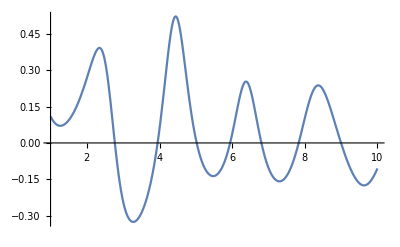

```mathematica
Plot[DipoleV2LargeN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y],{k,1,10}]
```

### Manipulate

```mathematica
ClearAll[time,tabLarge];
time=AbsoluteTime[];
tabLarge=Table[
ClearAll[x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
{{k,by,rA,rB,rAθ,rBθ},DipoleV2LargeN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},
{k,1,10,0.1},{by,0,5,1(*0.1*)},{rA,0.1,4,1(*0.2*)},{rB,0.1,4,1(*0.2*)},{rAθ,π/10,2π,π/2},{rBθ,π/10,2π,(*0.1*)π/2}]//Quiet;
AbsoluteTime[]-time
```

506.8201271

```mathematica
Flatten[tabLarge,1]
```

{1,2,{3}}

```mathematica
ClearAll[tabLarge1];
tabLarge1=Flatten[tabLarge,5];
```

```mathematica
ClearAll[tabLargeFun];
tabLargeFun=Interpolation[tabLarge1/.Indeterminate:>$Failed,InterpolationOrder->1];
```

```mathematica
Manipulate[{Show[Graphics[{Red,Disk[{rA/2 Cos[rAθ],by+rA/2 Sin[rAθ]},0.08]}],Graphics[{Blue,Disk[{-rA/2 Cos[rAθ],by-rA/2 Sin[rAθ]},0.08]}],Graphics[Line[{{rA/2 Cos[rAθ],by+rA/2 Sin[rAθ]},{-rA/2 Cos[rAθ],by-rA/2 Sin[rAθ]}}]],Graphics[{Red,Thick,Circle[{rB/2 Cos[rBθ],rB/2 Sin[rBθ]},0.08]}],Graphics[{Blue,Thick,Circle[{-rB/2 Cos[rBθ],-rB/2 Sin[rBθ]},0.08]}],Graphics[Line[{{rB/2 Cos[rBθ],rB/2 Sin[rBθ]},{-rB/2 Cos[rBθ],-rB/2 Sin[rBθ]}}]],Graphics[{Dashed,Line[{{0,0},{0,by}}]}],PlotRange->{{-3,3},{-3,8}},ImageSize->Medium,Frame->True],Plot[tabLargeFun[k,by,rA,rB,rAθ,rBθ],{k,1,10},PlotRange->{{1,10},{-0.5,0.5}},Frame->True,FrameLabel->{"kT","v_2"},ImageSize->Large]},{by,0,5,1(*0.1*)},{rA,0.1,4,1(*0.2*)},{rB,0.1,4,1(*0.2*)},{rAθ,π/10,3/2 π+π/10,π/2},{rBθ,π/10,3/2 π+π/10,(*0.1*)π/2}]//Quiet
```

### b

```mathematica
Getv2kT[k_,b_,rA_,rAθ_,rB_,rBθ_]:=Module[{bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y},
bx=b;
by=0.0;
x1x=bx/2+rA/2 Cos[rAθ];
x1y=by/2+rA/2 Sin[rAθ];
x2x=bx/2-rA/2 Cos[rAθ];
x2y=by/2-rA/2 Sin[rAθ];
x3x=-bx/2+rB/2 Cos[rBθ];
x3y=-by/2+rB/2 Sin[rBθ];
x4x=-bx/2-rB/2 Cos[rBθ];
x4y=-by/2-rB/2 Sin[rBθ];
DipoleV2LargeN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]
]
```

## b = 2

```mathematica
v2b20={{0.25,{-0.06294322741979848,-5.872321911797908*^-14}},{0.5,{-0.24189847126191794,-9.807551961406356*^-14}},{0.75,{-0.48454430255054487,2.2667164790300553*^-12}},{1.,{-0.6800785363396218,3.4978220482221835*^-16}},{1.25,{-0.7220912766079246,2.4983846780752516*^-16}},{1.5,{-0.650731830888267,-1.1387042913052963*^-16}},{1.75,{-0.5698212354744296,7.270017905940325*^-9}},{2.,{-0.5208747233243994,-4.962528455771066*^-11}},{2.25,{-0.5038285007534246,2.572975163973258*^-16}},{2.5,{-0.5108651725283526,-3.6685740814896163*^-17}},{2.75,{-0.5359088562216001,1.0752769076388552*^-17}},{3.,{-0.5747349714667126,-5.156639452737525*^-11}},{3.25,{-0.6231660710887356,-5.5260154113042726*^-11}},{3.5,{-0.6747391729334864,-4.817749058863643*^-9}},{3.75,{-0.7181193014223666,-5.096793214093726*^-16}},{4.,{-0.7356515260639354,4.562421243460781*^-11}},{4.25,{-0.7068377906836053,1.5812152705665003*^-10}},{4.5,{-0.6200397671962029,-2.961058277449802*^-10}},{4.75,{-0.48578306524934883,9.089602848604425*^-10}},{5.,{-0.334779210077128,7.184618206596412*^-10}},{5.25,{-0.19940392339034865,6.109210383218498*^-10}},{5.5,{-0.09862110608487162,1.1568971325936654*^-10}},{5.75,{-0.037629584808339014,-1.59247211137254*^-7}},{6.,{-0.014591830726602193,-7.964591998488446*^-8}},{6.25,{-0.02589113512522865,-8.520396403330992*^-9}},{6.5,{-0.06648030216450584,5.121406215487558*^-9}},{6.75,{-0.12219534081661644,4.675102462664738*^-9}},{7.,{-0.1506596938977829,-6.653650617568884*^-9}},{7.25,{-0.08351907572346967,-7.279697153350364*^-9}},{7.5,{0.07351684868684566,-7.187975099852266*^-7}},{7.75,{0.21315703822109988,-4.768282588361576*^-9}},{8.,{0.2794788117447774,4.509993543480511*^-9}},{8.25,{0.28354887557304587,3.4201174803693674*^-7}},{8.5,{0.24410348740864138,3.2793812314154096*^-9}},{8.75,{0.16975516203657443,1.3941639784470171*^-8}},{9.,{0.06115678697680605,-6.158505198188955*^-9}},{9.25,{-0.08326507912618733,1.1007489713600945*^-9}},{9.5,{-0.2571210409856718,-2.693396891221436*^-8}},{9.75,{-0.42852210021658116,8.656653418891017*^-9}},{10.,{-0.530749482927675,1.1991728842356803*^-8}},{10.25,{-0.5054459829067915,-2.28123805971069*^-8}},{10.5,{-0.37253524526226967,4.518471010902129*^-9}},{10.75,{-0.20791915697739471,-3.6464296097760344*^-8}},{11.,{-0.0682471797412982,1.9037880247406803*^-8}},{11.25,{0.027885219884035483,7.195414216127103*^-9}},{11.5,{0.08099214076241602,-2.9519283867048526*^-8}},{11.75,{0.09531902142089092,-1.539245176228123*^-8}},{12.,{0.07303150974721256,-7.584466563659315*^-8}},{12.25,{0.01390534016913221,-1.3338237891310884*^-7}},{12.5,{-0.0790213103481187,-1.4255344027088598*^-7}},{12.75,{-0.18233380986642045,-9.246313273463266*^-9}},{13.,{-0.23149069368658604,-7.385189219620484*^-9}},{13.25,{-0.1631330325050519,0.000011533849127017156}},{13.5,{-0.014349447755094754,4.307972012870345*^-8}},{13.75,{0.12469871960484381,1.1005108650760391*^-7}},{14.,{0.21272690232622468,-7.47863493307385*^-8}},{14.25,{0.24954399283555537,3.955983105976257*^-7}},{14.5,{0.24296605442241073,6.184276638840328*^-8}},{14.75,{0.19686064928461325,-3.1443103914760433*^-7}},{15.,{0.11068912238492895,2.902138022082587*^-8}},{15.25,{-0.01563043014371366,-2.8991147563658828*^-8}},{15.5,{-0.1700461276571382,1.4290615423408356*^-8}},{15.75,{-0.3134205946534458,-3.6586914747695166*^-7}},{16.,{-0.3858421202211369,-5.599714401436502*^-7}},{16.25,{-0.35708125713994454,-1.455416319384827*^-7}},{16.5,{-0.2582446192832246,9.487655565974058*^-8}},{16.75,{-0.14268739967635663,-3.08041240584178*^-7}},{17.,{-0.044339135713777976,-4.951558803240745*^-7}},{17.25,{0.02461714514783369,-1.8506868489498085*^-7}},{17.5,{0.06258721953101362,1.6448695112724287*^-7}},{17.75,{0.0705554180522356,8.380290820798926*^-7}},{18.,{0.04966711758307086,1.0715545063814352*^-6}},{18.25,{0.002709486448495187,8.974236072697144*^-7}},{18.5,{-0.06020492901229033,2.141314165578874*^-6}},{18.75,{-0.11442086492902735,-2.5253281268175955*^-6}},{19.,{-0.12558534475834957,-5.623738938645738*^-6}},{19.25,{-0.07835197700979778,-1.816825529239655*^-6}},{19.5,{0.00548526005581421,-6.651141506008074*^-7}},{19.75,{0.09071369124051476,-1.2673220496216533*^-6}},{20.,{0.1547768904773603,2.4172920017137556*^-7}},{20.25,{0.18966365468653157,8.794934170998154*^-9}},{20.5,{0.19368400332001778,5.738993216011659*^-7}},{20.75,{0.16666954012832896,-2.2986127464561347*^-7}},{21.,{0.10959022250044127,-5.666023778862234*^-7}},{21.25,{0.028194659156818406,-6.130940827120786*^-7}},{21.5,{-0.06340099040738281,8.730536472610196*^-7}},{21.75,{-0.14243897513144396,3.133458694315894*^-6}},{22.,{-0.18785308061251765,7.078895193830209*^-7}},{22.25,{-0.19316964458001137,-2.7821864462356767*^-6}},{22.5,{-0.16721112714985586,-9.433836998008276*^-7}},{22.75,{-0.12611941980518482,5.683253342228982*^-6}},{23.,{-0.08276295845798627,4.12023584865759*^-6}},{23.25,{-0.0452933207156625,-0.00004570340855019165}},{23.5,{-0.017735331742114287,-9.075615787723264*^-6}},{23.75,{-0.0014710078976876248,-7.711380419536145*^-7}},{24.,{0.004207762544797663,1.6392459718001695*^-6}},{24.25,{0.0019640140411407024,4.057027062705144*^-7}},{24.5,{-0.0036413484619243746,6.981744394960065*^-6}},{24.75,{-0.007074661146851558,8.224059001514674*^-6}},{25.,{-0.0038186068467083284,0.00003589812211751707}},{25.25,{0.007129402564893433,-0.0000100276432169617}},{25.5,{0.02622177591886605,-4.671121772801215*^-6}},{25.75,{0.04948317887911058,7.1686424044688035*^-6}},{26.,{0.07303292986617704,4.017299343340596*^-6}},{26.25,{0.0929312730670476,-0.000017154247732977316}},{26.5,{0.10561725321750384,-9.921865846817033*^-6}},{26.75,{0.10820024775092153,8.40263122427552*^-6}},{27.,{0.09912637011676095,0.00003315702779153328}},{27.25,{0.07861467277877875,0.00001830087660803843}},{27.5,{0.04854287192025461,-0.000017289939845689203}},{27.75,{0.011738626857271613,-3.4299906116457035*^-6}},{28.,{-0.028715192370927428,6.704084108510185*^-6}},{28.25,{-0.0694833421654259,-5.803150650880738*^-6}},{28.5,{-0.10681721328848023,7.264025347662797*^-6}},{28.75,{-0.13581403182319846,-5.498983693225244*^-6}},{29.,{-0.15078108183839106,-0.00001185452562217052}},{29.25,{-0.146785231134886,2.09209154841429*^-6}},{29.5,{-0.12215070230737883,-0.000030358145685716664}},{29.75,{-0.0808648199011981,-0.000028040786433457567}},{30.,{-0.03211246877109101,0.000010650899384681635}}};
```

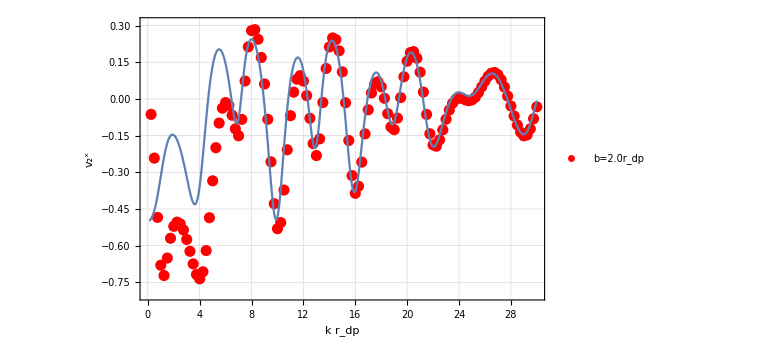

```mathematica
Show[{ListLinePlot[{Transpose[{v2b20[[All,1]],Re[v2b20[[All,2,1]]]}]},PlotRange->{{0,30},{-0.8,0.31}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"b=2.0r_dp","b=0.5r_dp","b=1.0r_dp","b=1.5r_dp","b=2.0r_dp"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k r_dp","v_2^x"}],Plot[Getv2kT[k,2.0,1.0,π/2,1.0,π/2],{k,.1,30}]}]
```

```mathematica
Length[v2b20]
```

120

```mathematica
Table[{v2b20[[All,1,i]],Re[v2b20[[All,2,1,i]]-Getv2kT[v2b20[[All,1,i]],2.0,1.0,π/2,1.0,π/2]]},{i,1,Length[v2b20]}]
```

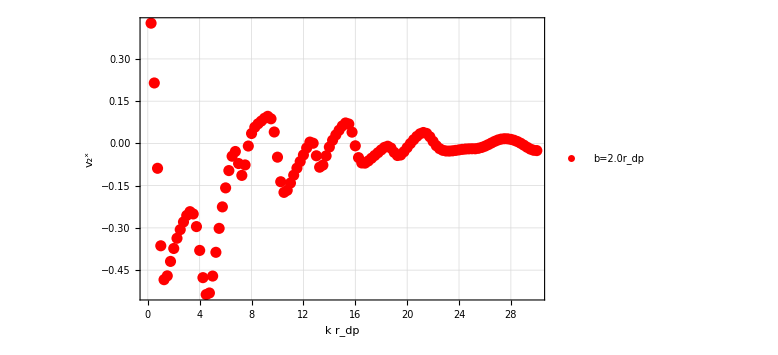

```mathematica
ListLinePlot[Table[{v2b20[[All,1]][[i]],Re[v2b20[[All,2,1]][[i]]-Getv2kT[v2b20[[All,1]][[i]],2.0,1.0,π/2,1.0,π/2]]},{i,1,Length[v2b20]}],(*PlotRange->{{0,30},{-0.8,0.31}},*)
GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"b=2.0r_dp","b=0.5r_dp","b=1.0r_dp","b=1.5r_dp","b=2.0r_dp"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k r_dp","v_2^x"}]
```